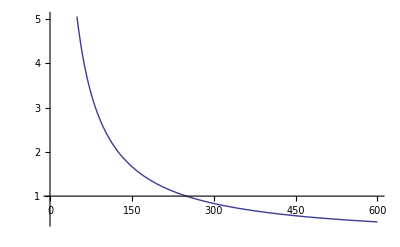

-0.0375

{4.62616,4.55488}

{-997.284,-1001.17}

```mathematica
T=1;t=.97;r=0;μ=.01+r;σ=.2;γ1=.001;γ=γ1 Exp[-T r];d=Exp[-(T-t) r];
S1=600;op[S_]:=(μ-r)/(γ σ^2 S)d
zeroRemainder[S_]:=(μ-r)/γ((T-t)/2-Log[S]/σ^2)
Plot[op[S],{S,1,S1}]
Table[{S,op[S]},{S,1,S1,S1/500}]//MatrixForm//N;
-(μ-r)^2(T-t)/(2 σ^2 γ)d
a={54.040520140622995,54.886134118350562};
op/@a
zeroRemainder/@a
```

```mathematica
u[p_,γ_]:=1/γ Log[p Exp[γ/p]+(1-p)Exp[-γ/(1-p)]]
```

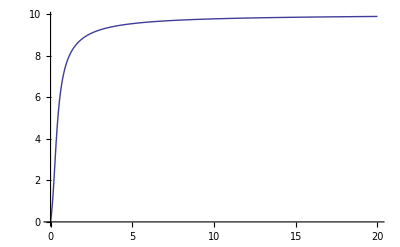

```mathematica
Plot[u[.1,x],{x,.0001,20},PlotRange->All]
```